```mathematica
j
```

j

```mathematica
Na=50;
n=14;
p=0.5;
q=0.5;
P[x_,n_]:=Binomial[n,x]*p^x*q^(n-x);
```

```mathematica
data =Table[20*Na*P[x,n],{x,0,n,1}];
exact =ListPlot[Table[20*Na*P[x,n],{x,0,n,1}],Joined->True,InterpolationOrder->2, Mesh->Full,PlotStyle->{Orange, PointSize[Large], Thick}];
exactbars = BarChart[data, AxesLabel->{"Slot", "#Balls"},ChartLabels->Range[n+1]];
data
Show[exactbars, exact,PlotRange->All]
```

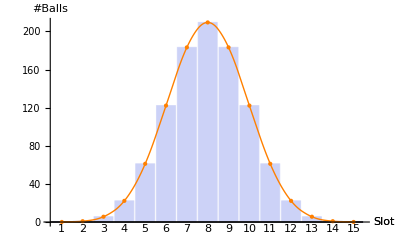

```mathematica
{0.06103515625,0.8544921875,5.55419921875,22.216796875,61.09619140625,122.1923828125,183.28857421875,209.47265625,183.28857421875,122.1923828125,61.09619140625,22.216796875,5.55419921875,0.8544921875,0.06103515625}
```

```mathematica
sheet =Import[FileNameJoin[{NotebookDirectory[],"Messwerte Galton-Brett.xls"}]][[1]];
total=sheet[[25]][[3 ;; 17]];
```

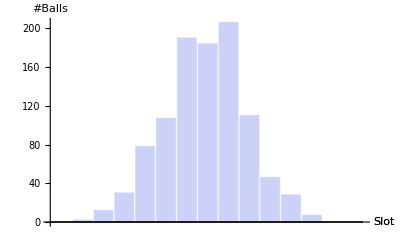

Directive[Bold]

```mathematica
mb=BarChart[total,AxesLabel->{"Slot", "#Balls"},LabelStyle->Directive[FontFamily->"Helvetica"]]
Directive[Bold]
```